```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=80;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

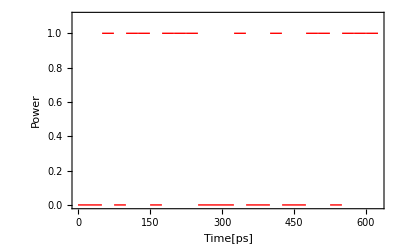

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1.1}]
```

```mathematica
∫_0^(bit*25*10^-12) signal[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-1/(2 f π)ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000))

```mathematica
fc[f_]:=-1/(2 f π)ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000))
```

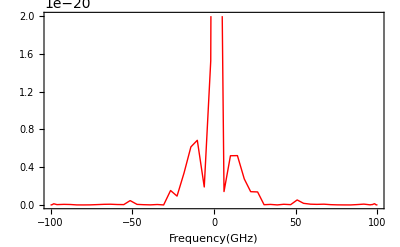

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)",},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

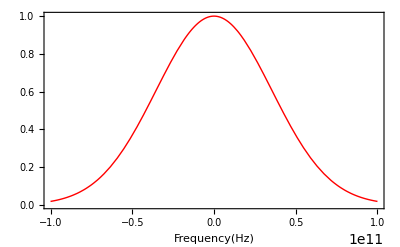

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

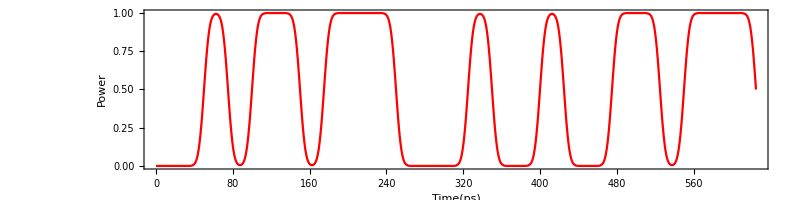

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
(*f[x_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]*)
```

```mathematica
(*max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]*)
```

## Impulse Responce for Fiber Dispersion

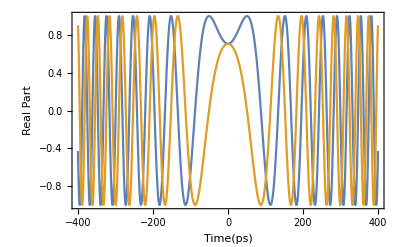

```mathematica
hdis[t_]:=(*1/(√(2*Pi*β2*L))*10^6**)Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
(*hcmp[t_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(t^2/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]*)
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]*)
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

-Graphics-

## Simulation

```mathematica
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*hdis2[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

24.0754-16.6179 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,29.2537},{-99.5,29.0662},{-99.,28.8942},{-98.5,28.7349},{-98.,28.5858},{-97.5,28.4445},{-97.,28.3087},{-96.5,28.1766},{-96.,28.0467},{-95.5,27.9177},{-95.,27.7891},{-94.5,27.6606},{-94.,27.5324},{-93.5,27.4054},{-93.,27.2808},{-92.5,27.1604},{-92.,27.0465},{-91.5,26.9416},{-91.,26.8488},{-90.5,26.7717},{-90.,26.7138},{-89.5,26.6791},{-89.,26.6715},{-88.5,26.6952},{-88.,26.754},{-87.5,26.8519},{-87.,26.9923},{-86.5,27.1783},{-86.,27.4128},{-85.5,27.6978},{-85.,28.035},{-84.5,28.4253},{-84.,28.8691},{-83.5,29.366},{-83.,29.9151},{-82.5,30.5149},{-82.,31.1633},{-81.5,31.8578},{-81.,32.5954},{-80.5,33.3727},{-80.,34.186},{-79.5,35.0313},{-79.,35.9042},{-78.5,36.8004},{-78.,37.7152},{-77.5,38.6437},{-77.,39.5809},{-76.5,40.5218},{-76.,41.4613},{-75.5,42.394},{-75.,43.3146},{-74.5,44.2179},{-74.,45.0986},{-73.5,45.9512},{-73.,46.7706},{-72.5,47.5515},{-72.,48.289},{-71.5,48.9782},{-71.,49.6144},{-70.5,50.1932},{-70.,50.7105},{-69.5,51.1625},{-69.,51.5459},{-68.5,51.8579},{-68.,52.0961},{-67.5,52.2589},{-67.,52.345},{-66.5,52.3542},{-66.,52.287},{-65.5,52.1445},{-65.,51.9291},{-64.5,51.6439},{-64.,51.2931},{-63.5,50.882},{-63.,50.4172},{-62.5,49.9061},{-62.,49.3578},{-61.5,48.7821},{-61.,48.1902},{-60.5,47.5943},{-60.,47.0076},{-59.5,46.4441},{-59.,45.9181},{-58.5,45.4442},{-58.,45.0369},{-57.5,44.7098},{-57.,44.4754},{-56.5,44.3443},{-56.,44.3252},{-55.5,44.4238},{-55.,44.643},{-54.5,44.9823},{-54.,45.4384},{-53.5,46.0048},{-53.,46.6723},{-52.5,47.4297},{-52.,48.2638},{-51.5,49.1601},{-51.,50.1034},{-50.5,51.0781},{-50.,52.0687},{-49.5,53.0598},{-49.,54.0371},{-48.5,54.9866},{-48.,55.8956},{-47.5,56.7526},{-47.,57.5473},{-46.5,58.2705},{-46.,58.9146},{-45.5,59.4735},{-45.,59.9425},{-44.5,60.3185},{-44.,60.5996},{-43.5,60.786},{-43.,60.8791},{-42.5,60.882},{-42.,60.7995},{-41.5,60.6379},{-41.,60.4049},{-40.5,60.11},{-40.,59.764},{-39.5,59.3789},{-39.,58.9682},{-38.5,58.5461},{-38.,58.1277},{-37.5,57.7287},{-37.,57.3646},{-36.5,57.0511},{-36.,56.8027},{-35.5,56.6329},{-35.,56.5536},{-34.5,56.5743},{-34.,56.7023},{-33.5,56.9417},{-33.,57.2938},{-32.5,57.7569},{-32.,58.3263},{-31.5,58.9945},{-31.,59.7517},{-30.5,60.586},{-30.,61.484},{-29.5,62.4311},{-29.,63.4121},{-28.5,64.4114},{-28.,65.4136},{-27.5,66.4035},{-27.,67.3664},{-26.5,68.2886},{-26.,69.1573},{-25.5,69.9605},{-25.,70.6878},{-24.5,71.3295},{-24.,71.8775},{-23.5,72.3248},{-23.,72.6657},{-22.5,72.8957},{-22.,73.0115},{-21.5,73.0112},{-21.,72.8938},{-20.5,72.6596},{-20.,72.31},{-19.5,71.8473},{-19.,71.275},{-18.5,70.5972},{-18.,69.8191},{-17.5,68.9465},{-17.,67.9861},{-16.5,66.945},{-16.,65.831},{-15.5,64.6522},{-15.,63.4172},{-14.5,62.1348},{-14.,60.8137},{-13.5,59.4632},{-13.,58.0919},{-12.5,56.7087},{-12.,55.3221},{-11.5,53.9401},{-11.,52.5703},{-10.5,51.2197},{-10.,49.8946},{-9.5,48.6006},{-9.,47.3424},{-8.5,46.1239},{-8.,44.9481},{-7.5,43.8171},{-7.,42.7319},{-6.5,41.6932},{-6.,40.7004},{-5.5,39.7525},{-5.,38.8481},{-4.5,37.9851},{-4.,37.1615},{-3.5,36.3748},{-3.,35.623},{-2.5,34.9038},{-2.,34.2158},{-1.5,33.5574},{-1.,32.9281},{-0.5,32.3276},{0.,31.7564},{0.5,31.2156},{1.,30.707},{1.5,30.2329},{2.,29.7963},{2.5,29.4004},{3.,29.0488},{3.5,28.7453},{4.,28.4935},{4.5,28.2971},{5.,28.1591},{5.5,28.0822},{6.,28.0684},{6.5,28.1188},{7.,28.2337},{7.5,28.4124},{8.,28.6537},{8.5,28.9552},{9.,29.3138},{9.5,29.7261},{10.,30.188},{10.5,30.6951},{11.,31.2428},{11.5,31.8265},{12.,32.4417},{12.5,33.0837},{13.,33.7484},{13.5,34.4317},{14.,35.1298},{14.5,35.8392},{15.,36.5568},{15.5,37.2799},{16.,38.0059},{16.5,38.7326},{17.,39.4584},{17.5,40.1815},{18.,40.9008},{18.5,41.6155},{19.,42.3248},{19.5,43.0286},{20.,43.7269},{20.5,44.42},{21.,45.1086},{21.5,45.7937},{22.,46.4766},{22.5,47.1591},{23.,47.8432},{23.5,48.5311},{24.,49.2257},{24.5,49.9297},{25.,50.6465},{25.5,51.3794},{26.,52.132},{26.5,52.9079},{27.,53.711},{27.5,54.5446},{28.,55.4124},{28.5,56.3174},{29.,57.2625},{29.5,58.25},{30.,59.2818},{30.5,60.3589},{31.,61.4819},{31.5,62.6505},{32.,63.8636},{32.5,65.1193},{33.,66.4149},{33.5,67.7469},{34.,69.1111},{34.5,70.5024},{35.,71.9153},{35.5,73.3437},{36.,74.7807},{36.5,76.2196},{37.,77.6528},{37.5,79.0731},{38.,80.4727},{38.5,81.8443},{39.,83.1803},{39.5,84.4737},{40.,85.7176},{40.5,86.9056},{41.,88.0318},{41.5,89.0908},{42.,90.0779},{42.5,90.9891},{43.,91.8211},{43.5,92.5715},{44.,93.2386},{44.5,93.8217},{45.,94.3208},{45.5,94.7369},{46.,95.0719},{46.5,95.3283},{47.,95.5096},{47.5,95.6199},{48.,95.664},{48.5,95.6472},{49.,95.5756},{49.5,95.4553},{50.,95.2929},{50.5,95.095},{51.,94.8683},{51.5,94.6193},{52.,94.3542},{52.5,94.079},{53.,93.799},{53.5,93.5188},{54.,93.2426},{54.5,92.9736},{55.,92.7141},{55.5,92.4658},{56.,92.2295},{56.5,92.0052},{57.,91.7924},{57.5,91.5899},{58.,91.3961},{58.5,91.2093},{59.,91.0276},{59.5,90.8494},{60.,90.6732},{60.5,90.4984},{61.,90.3247},{61.5,90.153},{62.,89.9853},{62.5,89.8246},{63.,89.6755},{63.5,89.5437},{64.,89.4366},{64.5,89.3627},{65.,89.332},{65.5,89.3555},{66.,89.4455},{66.5,89.6144},{67.,89.8754},{67.5,90.2414},{68.,90.7248},{68.5,91.3373},{69.,92.0889},{69.5,92.9879},{70.,94.0404},{70.5,95.2501},{71.,96.6177},{71.5,98.1415},{72.,99.8168},{72.5,101.636},{73.,103.589},{73.5,105.664},{74.,107.847},{74.5,110.121},{75.,112.471},{75.5,114.876},{76.,117.321},{76.5,119.784},{77.,122.248},{77.5,124.695},{78.,127.105},{78.5,129.463},{79.,131.751},{79.5,133.954},{80.,136.058},{80.5,138.051},{81.,139.92},{81.5,141.655},{82.,143.249},{82.5,144.693},{83.,145.981},{83.5,147.11},{84.,148.077},{84.5,148.879},{85.,149.517},{85.5,149.992},{86.,150.306},{86.5,150.463},{87.,150.466},{87.5,150.32},{88.,150.032},{88.5,149.607},{89.,149.053},{89.5,148.376},{90.,147.583},{90.5,146.681},{91.,145.676},{91.5,144.574},{92.,143.381},{92.5,142.103},{93.,140.742},{93.5,139.302},{94.,137.786},{94.5,136.195},{95.,134.53},{95.5,132.79},{96.,130.974},{96.5,129.081},{97.,127.107},{97.5,125.052},{98.,122.911},{98.5,120.683},{99.,118.365},{99.5,115.955},{100.,113.453},{100.5,110.86},{101.,108.178},{101.5,105.411},{102.,102.566},{102.5,99.6524},{103.,96.6838},{103.5,93.6768},{104.,90.6529},{104.5,87.6384},{105.,84.6652},{105.5,81.7713},{106.,79.0011},{106.5,76.4053},{107.,74.0406},{107.5,71.9683},{108.,70.2519},{108.5,68.954},{109.,68.1315},{109.5,67.8308},{110.,68.0832},{110.5,68.9011},{111.,70.2773},{111.5,72.1861},{112.,74.5864},{112.5,77.4262},{113.,80.647},{113.5,84.188},{114.,87.9887},{114.5,91.9912},{115.,96.1412},{115.5,100.389},{116.,104.688},{116.5,108.999},{117.,113.283},{117.5,117.507},{118.,121.643},{118.5,125.663},{119.,129.544},{119.5,133.265},{120.,136.81},{120.5,140.163},{121.,143.311},{121.5,146.243},{122.,148.953},{122.5,151.433},{123.,153.679},{123.5,155.691},{124.,157.466},{124.5,159.008},{125.,160.32},{125.5,161.406},{126.,162.272},{126.5,162.928},{127.,163.381},{127.5,163.643},{128.,163.723},{128.5,163.635},{129.,163.391},{129.5,163.004},{130.,162.488},{130.5,161.858},{131.,161.127},{131.5,160.31},{132.,159.42},{132.5,158.472},{133.,157.478},{133.5,156.452},{134.,155.406},{134.5,154.35},{135.,153.297},{135.5,152.257},{136.,151.237},{136.5,150.248},{137.,149.296},{137.5,148.389},{138.,147.534},{138.5,146.736},{139.,146.001},{139.5,145.334},{140.,144.74},{140.5,144.222},{141.,143.785},{141.5,143.434},{142.,143.171},{142.5,143.001},{143.,142.928},{143.5,142.954},{144.,143.083},{144.5,143.317},{145.,143.659},{145.5,144.111},{146.,144.673},{146.5,145.346},{147.,146.13},{147.5,147.023},{148.,148.022},{148.5,149.124},{149.,150.324},{149.5,151.617},{150.,152.995},{150.5,154.45},{151.,155.974},{151.5,157.556},{152.,159.187},{152.5,160.853},{153.,162.545},{153.5,164.248},{154.,165.952},{154.5,167.643},{155.,169.309},{155.5,170.937},{156.,172.516},{156.5,174.033},{157.,175.479},{157.5,176.841},{158.,178.112},{158.5,179.282},{159.,180.343},{159.5,181.289},{160.,182.114},{160.5,182.813},{161.,183.382},{161.5,183.819},{162.,184.124},{162.5,184.295},{163.,184.333},{163.5,184.242},{164.,184.025},{164.5,183.685},{165.,183.23},{165.5,182.665},{166.,181.998},{166.5,181.24},{167.,180.399},{167.5,179.486},{168.,178.514},{168.5,177.494},{169.,176.441},{169.5,175.368},{170.,174.29},{170.5,173.222},{171.,172.179},{171.5,171.176},{172.,170.23},{172.5,169.356},{173.,168.568},{173.5,167.882},{174.,167.311},{174.5,166.868},{175.,166.565},{175.5,166.412},{176.,166.419},{176.5,166.593},{177.,166.938},{177.5,167.46},{178.,168.16},{178.5,169.037},{179.,170.09},{179.5,171.314},{180.,172.704},{180.5,174.252},{181.,175.95},{181.5,177.788},{182.,179.754},{182.5,181.835},{183.,184.02},{183.5,186.293},{184.,188.643},{184.5,191.053},{185.,193.51},{185.5,196.},{186.,198.508},{186.5,201.02},{187.,203.524},{187.5,206.005},{188.,208.452},{188.5,210.851},{189.,213.192},{189.5,215.463},{190.,217.654},{190.5,219.754},{191.,221.755},{191.5,223.648},{192.,225.425},{192.5,227.077},{193.,228.599},{193.5,229.982},{194.,231.221},{194.5,232.311},{195.,233.245},{195.5,234.019},{196.,234.629},{196.5,235.07},{197.,235.337},{197.5,235.428},{198.,235.339},{198.5,235.066},{199.,234.608},{199.5,233.96},{200.,233.12},{200.5,232.087},{201.,230.857},{201.5,229.431},{202.,227.805},{202.5,225.978},{203.,223.951},{203.5,221.722},{204.,219.292},{204.5,216.661},{205.,213.83},{205.5,210.801},{206.,207.575},{206.5,204.156},{207.,200.547},{207.5,196.752},{208.,192.776},{208.5,188.625},{209.,184.306},{209.5,179.826},{210.,175.194},{210.5,170.419},{211.,165.51},{211.5,160.48},{212.,155.341},{212.5,150.104},{213.,144.784},{213.5,139.396},{214.,133.955},{214.5,128.477},{215.,122.979},{215.5,117.479},{216.,111.994},{216.5,106.545},{217.,101.149},{217.5,95.8269},{218.,90.5978},{218.5,85.482},{219.,80.4996},{219.5,75.6706},{220.,71.0148},{220.5,66.5512},{221.,62.2984},{221.5,58.2737},{222.,54.4926},{222.5,50.9687},{223.,47.7124},{223.5,44.7305},{224.,42.0256},{224.5,39.5946},{225.,37.4286},{225.5,35.5129},{226.,33.8265},{226.5,32.3435},{227.,31.0337},{227.5,29.865},{228.,28.8043},{228.5,27.8199},{229.,26.8824},{229.5,25.966},{230.,25.0495},{230.5,24.1163},{231.,23.1547},{231.5,22.1578},{232.,21.1235},{232.5,20.0544},{233.,18.9572},{233.5,17.8432},{234.,16.7276},{234.5,15.6302},{235.,14.5748},{235.5,13.5893},{236.,12.705},{236.5,11.9548},{237.,11.3707},{237.5,10.9783},{238.,10.793},{238.5,10.8155},{239.,11.0329},{239.5,11.4229},{240.,11.9604},{240.5,12.6236},{241.,13.3981},{241.5,14.2791},{242.,15.2712},{242.5,16.3879},{243.,17.6501},{243.5,19.0835},{244.,20.7163},{244.5,22.577},{245.,24.692},{245.5,27.0841},{246.,29.7713},{246.5,32.7668},{247.,36.0786},{247.5,39.71},{248.,43.6602},{248.5,47.9247},{249.,52.4958},{249.5,57.3629},{250.,62.5129},{250.5,67.9306},{251.,73.5986},{251.5,79.4978},{252.,85.6076},{252.5,91.9057},{253.,98.3685},{253.5,104.971},{254.,111.689},{254.5,118.493},{255.,125.358},{255.5,132.256},{256.,139.157},{256.5,146.032},{257.,152.854},{257.5,159.594},{258.,166.222},{258.5,172.711},{259.,179.033},{259.5,185.161},{260.,191.069},{260.5,196.732},{261.,202.125},{261.5,207.228},{262.,212.017},{262.5,216.475},{263.,220.582},{263.5,224.323},{264.,227.684},{264.5,230.652},{265.,233.218},{265.5,235.372},{266.,237.11},{266.5,238.427},{267.,239.322},{267.5,239.795},{268.,239.85},{268.5,239.492},{269.,238.727},{269.5,237.566},{270.,236.019},{270.5,234.099},{271.,231.823},{271.5,229.208},{272.,226.271},{272.5,223.033},{273.,219.517},{273.5,215.745},{274.,211.741},{274.5,207.53},{275.,203.139},{275.5,198.593},{276.,193.92},{276.5,189.146},{277.,184.3},{277.5,179.406},{278.,174.492},{278.5,169.583},{279.,164.703},{279.5,159.875},{280.,155.122},{280.5,150.462},{281.,145.914},{281.5,141.493},{282.,137.212},{282.5,133.082},{283.,129.11},{283.5,125.301},{284.,121.657},{284.5,118.178},{285.,114.861},{285.5,111.699},{286.,108.686},{286.5,105.812},{287.,103.066},{287.5,100.436},{288.,97.9091},{288.5,95.4736},{289.,93.1166},{289.5,90.8261},{290.,88.591},{290.5,86.4012},{291.,84.2479},{291.5,82.1238},{292.,80.023},{292.5,77.9413},{293.,75.8759},{293.5,73.8256},{294.,71.7905},{294.5,69.7719},{295.,67.7725},{295.5,65.7957},{296.,63.8458},{296.5,61.9277},{297.,60.0467},{297.5,58.208},{298.,56.4172},{298.5,54.6793},{299.,52.9993},{299.5,51.3813},{300.,49.829},{300.5,48.3451},{301.,46.9317},{301.5,45.5899},{302.,44.3201},{302.5,43.122},{303.,41.9947},{303.5,40.9367},{304.,39.9463},{304.5,39.0219},{305.,38.1619},{305.5,37.365},{306.,36.6304},{306.5,35.9581},{307.,35.3485},{307.5,34.8032},{308.,34.3239},{308.5,33.9136},{309.,33.5751},{309.5,33.3118},{310.,33.127},{310.5,33.0233},{311.,33.0029},{311.5,33.067},{312.,33.2153},{312.5,33.4462},{313.,33.7566},{313.5,34.1418},{314.,34.5955},{314.5,35.1101},{315.,35.677},{315.5,36.2865},{316.,36.9282},{316.5,37.5914},{317.,38.265},{317.5,38.9382},{318.,39.6002},{318.5,40.2403},{319.,40.8487},{319.5,41.4156},{320.,41.9323},{320.5,42.3904},{321.,42.7823},{321.5,43.1012},{322.,43.3408},{322.5,43.4958},{323.,43.5613},{323.5,43.5335},{324.,43.4092},{324.5,43.1858},{325.,42.8618},{325.5,42.4362},{326.,41.9092},{326.5,41.2817},{327.,40.5558},{327.5,39.7349},{328.,38.8238},{328.5,37.8289},{329.,36.759},{329.5,35.6252},{330.,34.4422},{330.5,33.2284},{331.,32.0073},{331.5,30.8082},{332.,29.6676},{332.5,28.6298},{333.,27.7469},{333.5,27.0776},{334.,26.6843},{334.5,26.6267},{335.,26.9551},{335.5,27.7029},{336.,28.883},{336.5,30.4877},{337.,32.4928},{337.5,34.864},{338.,37.562},{338.5,40.5473},{339.,43.782},{339.5,47.2312},{340.,50.8632},{340.5,54.6493},{341.,58.5629},{341.5,62.5796},{342.,66.6767},{342.5,70.8324},{343.,75.0261},{343.5,79.2376},{344.,83.4476},{344.5,87.6369},{345.,91.7871},{345.5,95.8798},{346.,99.8973},{346.5,103.822},{347.,107.637},{347.5,111.326},{348.,114.873},{348.5,118.264},{349.,121.483},{349.5,124.517},{350.,127.355},{350.5,129.984},{351.,132.394},{351.5,134.577},{352.,136.526},{352.5,138.234},{353.,139.696},{353.5,140.912},{354.,141.878},{354.5,142.597},{355.,143.071},{355.5,143.305},{356.,143.305},{356.5,143.081},{357.,142.642},{357.5,142.003},{358.,141.178},{358.5,140.183},{359.,139.037},{359.5,137.761},{360.,136.376},{360.5,134.907},{361.,133.377},{361.5,131.811},{362.,130.236},{362.5,128.677},{363.,127.16},{363.5,125.708},{364.,124.344},{364.5,123.088},{365.,121.958},{365.5,120.967},{366.,120.125},{366.5,119.438},{367.,118.906},{367.5,118.526},{368.,118.289},{368.5,118.183},{369.,118.192},{369.5,118.295},{370.,118.47},{370.5,118.692},{371.,118.936},{371.5,119.174},{372.,119.379},{372.5,119.525},{373.,119.587},{373.5,119.54},{374.,119.361},{374.5,119.031},{375.,118.53},{375.5,117.842},{376.,116.954},{376.5,115.855},{377.,114.536},{377.5,112.993},{378.,111.222},{378.5,109.224},{379.,107.003},{379.5,104.565},{380.,101.921},{380.5,99.0827},{381.,96.0682},{381.5,92.8983},{382.,89.5986},{382.5,86.1993},{383.,82.7361},{383.5,79.2505},{384.,75.7911},{384.5,72.4137},{385.,69.1818},{385.5,66.1672},{386.,63.4481},{386.5,61.1074},{387.,59.2281},{387.5,57.8863},{388.,57.1435},{388.5,57.0382},{389.,57.5804},{389.5,58.7499},{390.,60.5001},{390.5,62.7649},{391.,65.4671},{391.5,68.5261},{392.,71.8631},{392.5,75.4049},{393.,79.0852},{393.5,82.8456},{394.,86.6346},{394.5,90.4077},{395.,94.1263},{395.5,97.757},{396.,101.271},{396.5,104.643},{397.,107.852},{397.5,110.88},{398.,113.711},{398.5,116.331},{399.,118.731},{399.5,120.902},{400.,122.836},{400.5,124.528},{401.,125.975},{401.5,127.174},{402.,128.126},{402.5,128.831},{403.,129.29},{403.5,129.507},{404.,129.486},{404.5,129.232},{405.,128.753},{405.5,128.053},{406.,127.143},{406.5,126.031},{407.,124.726},{407.5,123.239},{408.,121.581},{408.5,119.765},{409.,117.802},{409.5,115.705},{410.,113.489},{410.5,111.168},{411.,108.757},{411.5,106.271},{412.,103.728},{412.5,101.142},{413.,98.5336},{413.5,95.919},{414.,93.3175},{414.5,90.7484},{415.,88.2315},{415.5,85.7872},{416.,83.4361},{416.5,81.1991},{417.,79.097},{417.5,77.1499},{418.,75.3775},{418.5,73.7977},{419.,72.4269},{419.5,71.2787},{420.,70.3639},{420.5,69.6896},{421.,69.259},{421.5,69.0713},{422.,69.1214},{422.5,69.4004},{423.,69.8959},{423.5,70.5926},{424.,71.473},{424.5,72.5179},{425.,73.7071},{425.5,75.0201},{426.,76.4363},{426.5,77.9357},{427.,79.4989},{427.5,81.1073},{428.,82.7434},{428.5,84.3907},{429.,86.0337},{429.5,87.658},{430.,89.2501},{430.5,90.7976},{431.,92.2887},{431.5,93.7127},{432.,95.0596},{432.5,96.3202},{433.,97.486},{433.5,98.5492},{434.,99.5028},{434.5,100.34},{435.,101.057},{435.5,101.646},{436.,102.106},{436.5,102.431},{437.,102.621},{437.5,102.672},{438.,102.586},{438.5,102.362},{439.,102.001},{439.5,101.507},{440.,100.883},{440.5,100.134},{441.,99.2662},{441.5,98.2882},{442.,97.2089},{442.5,96.0391},{443.,94.7911},{443.5,93.4789},{444.,92.118},{444.5,90.7256},{445.,89.3205},{445.5,87.9226},{446.,86.5536},{446.5,85.2357},{447.,83.992},{447.5,82.846},{448.,81.8206},{448.5,80.9381},{449.,80.2189},{449.5,79.6813},{450.,79.3403},{450.5,79.2074},{451.,79.2897},{451.5,79.5898},{452.,80.1055},{452.5,80.8303},{453.,81.7532},{453.5,82.8598},{454.,84.1326},{454.5,85.5518},{455.,87.096},{455.5,88.7429},{456.,90.4699},{456.5,92.2547},{457.,94.0757},{457.5,95.9121},{458.,97.7446},{458.5,99.555},{459.,101.327},{459.5,103.046},{460.,104.699},{460.5,106.273},{461.,107.761},{461.5,109.152},{462.,110.442},{462.5,111.624},{463.,112.697},{463.5,113.656},{464.,114.503},{464.5,115.237},{465.,115.86},{465.5,116.375},{466.,116.787},{466.5,117.099},{467.,117.318},{467.5,117.45},{468.,117.502},{468.5,117.48},{469.,117.392},{469.5,117.247},{470.,117.052},{470.5,116.815},{471.,116.545},{471.5,116.247},{472.,115.93},{472.5,115.601},{473.,115.267},{473.5,114.932},{474.,114.603},{474.5,114.284},{475.,113.98},{475.5,113.694},{476.,113.43},{476.5,113.19},{477.,112.977},{477.5,112.792},{478.,112.637},{478.5,112.512},{479.,112.42},{479.5,112.359},{480.,112.331},{480.5,112.337},{481.,112.377},{481.5,112.45},{482.,112.558},{482.5,112.701},{483.,112.879},{483.5,113.092},{484.,113.342},{484.5,113.627},{485.,113.948},{485.5,114.305},{486.,114.698},{486.5,115.126},{487.,115.588},{487.5,116.084},{488.,116.611},{488.5,117.168},{489.,117.753},{489.5,118.363},{490.,118.994},{490.5,119.645},{491.,120.309},{491.5,120.985},{492.,121.666},{492.5,122.348},{493.,123.026},{493.5,123.696},{494.,124.351},{494.5,124.986},{495.,125.595},{495.5,126.173},{496.,126.715},{496.5,127.214},{497.,127.665},{497.5,128.062},{498.,128.401},{498.5,128.676},{499.,128.882},{499.5,129.013},{500.,129.065},{500.5,129.033},{501.,128.912},{501.5,128.698},{502.,128.387},{502.5,127.973},{503.,127.455},{503.5,126.827},{504.,126.085},{504.5,125.228},{505.,124.252},{505.5,123.154},{506.,121.932},{506.5,120.586},{507.,119.113},{507.5,117.515},{508.,115.791},{508.5,113.944},{509.,111.977},{509.5,109.894},{510.,107.701},{510.5,105.406},{511.,103.019},{511.5,100.553},{512.,98.023},{512.5,95.4474},{513.,92.8482},{513.5,90.2515},{514.,87.6876},{514.5,85.1916},{515.,82.8034},{515.5,80.5679},{516.,78.5343},{516.5,76.7552},{517.,75.285},{517.5,74.178},{518.,73.4844},{518.5,73.2479},{519.,73.5017},{519.5,74.2658},{520.,75.546},{520.5,77.3332},{521.,79.6052},{521.5,82.3293},{522.,85.465},{522.5,88.9672},{523.,92.7888},{523.5,96.8828},{524.,101.203},{524.5,105.707},{525.,110.354},{525.5,115.107},{526.,119.932},{526.5,124.798},{527.,129.677},{527.5,134.544},{528.,139.376},{528.5,144.153},{529.,148.858},{529.5,153.475},{530.,157.991},{530.5,162.394},{531.,166.675},{531.5,170.826},{532.,174.841},{532.5,178.717},{533.,182.449},{533.5,186.037},{534.,189.48},{534.5,192.781},{535.,195.94},{535.5,198.962},{536.,201.851},{536.5,204.611},{537.,207.248},{537.5,209.768},{538.,212.177},{538.5,214.481},{539.,216.688},{539.5,218.802},{540.,220.831},{540.5,222.78},{541.,224.653},{541.5,226.455},{542.,228.191},{542.5,229.864},{543.,231.475},{543.5,233.027},{544.,234.52},{544.5,235.954},{545.,237.329},{545.5,238.644},{546.,239.896},{546.5,241.083},{547.,242.201},{547.5,243.249},{548.,244.222},{548.5,245.116},{549.,245.927},{549.5,246.653},{550.,247.289},{550.5,247.832},{551.,248.279},{551.5,248.627},{552.,248.873},{552.5,249.017},{553.,249.056},{553.5,248.989},{554.,248.816},{554.5,248.537},{555.,248.152},{555.5,247.663},{556.,247.069},{556.5,246.373},{557.,245.576},{557.5,244.68},{558.,243.687},{558.5,242.599},{559.,241.419},{559.5,240.148},{560.,238.788},{560.5,237.341},{561.,235.809},{561.5,234.193},{562.,232.494},{562.5,230.713},{563.,228.851},{563.5,226.909},{564.,224.888},{564.5,222.787},{565.,220.608},{565.5,218.35},{566.,216.015},{566.5,213.604},{567.,211.117},{567.5,208.556},{568.,205.923},{568.5,203.221},{569.,200.454},{569.5,197.624},{570.,194.736},{570.5,191.797},{571.,188.811},{571.5,185.787},{572.,182.732},{572.5,179.654},{573.,176.562},{573.5,173.468},{574.,170.38},{574.5,167.31},{575.,164.269},{575.5,161.267},{576.,158.317},{576.5,155.427},{577.,152.609},{577.5,149.871},{578.,147.222},{578.5,144.667},{579.,142.213},{579.5,139.862},{580.,137.617},{580.5,135.476},{581.,133.439},{581.5,131.499},{582.,129.651},{582.5,127.887},{583.,126.197},{583.5,124.569},{584.,122.992},{584.5,121.453},{585.,119.937},{585.5,118.432},{586.,116.923},{586.5,115.398},{587.,113.844},{587.5,112.25},{588.,110.607},{588.5,108.906},{589.,107.14},{589.5,105.306},{590.,103.399},{590.5,101.421},{591.,99.3714},{591.5,97.2558},{592.,95.0803},{592.5,92.8536},{593.,90.587},{593.5,88.2941},{594.,85.991},{594.5,83.696},{595.,81.4298},{595.5,79.215},{596.,77.0762},{596.5,75.0393},{597.,73.1314},{597.5,71.3801},{598.,69.8124},{598.5,68.4542},{599.,67.3289},{599.5,66.4568},{600.,65.8534},{600.5,65.5291},{601.,65.4885},{601.5,65.7302},{602.,66.2471},{602.5,67.0271},{603.,68.054},{603.5,69.3089},{604.,70.7708},{604.5,72.4183},{605.,74.2299},{605.5,76.1853},{606.,78.2652},{606.5,80.4525},{607.,82.7314},{607.5,85.0884},{608.,87.5112},{608.5,89.9896},{609.,92.5144},{609.5,95.0776},{610.,97.6719},{610.5,100.291},{611.,102.928},{611.5,105.578},{612.,108.234},{612.5,110.89},{613.,113.539},{613.5,116.174},{614.,118.787},{614.5,121.369},{615.,123.912},{615.5,126.406},{616.,128.84},{616.5,131.204},{617.,133.487},{617.5,135.677},{618.,137.762},{618.5,139.732},{619.,141.574},{619.5,143.277},{620.,144.83},{620.5,146.224},{621.,147.447},{621.5,148.493},{622.,149.351},{622.5,150.018},{623.,150.485},{623.5,150.751},{624.,150.811},{624.5,150.665},{625.,150.314},{625.5,149.76},{626.,149.006},{626.5,148.058},{627.,146.924},{627.5,145.613},{628.,144.136},{628.5,142.506},{629.,140.736},{629.5,138.843},{630.,136.843},{630.5,134.756},{631.,132.601},{631.5,130.398},{632.,128.167},{632.5,125.932},{633.,123.712},{633.5,121.529},{634.,119.402},{634.5,117.352},{635.,115.395},{635.5,113.546},{636.,111.818},{636.5,110.222},{637.,108.764},{637.5,107.449},{638.,106.278},{638.5,105.247},{639.,104.351},{639.5,103.582},{640.,102.931},{640.5,102.384},{641.,101.929},{641.5,101.551},{642.,101.236},{642.5,100.971},{643.,100.744},{643.5,100.542},{644.,100.357},{644.5,100.181},{645.,100.009},{645.5,99.8369},{646.,99.6655},{646.5,99.4964},{647.,99.3335},{647.5,99.1832},{648.,99.0536},{648.5,98.9544},{649.,98.8962},{649.5,98.8908},{650.,98.9497},{650.5,99.0847},{651.,99.3063},{651.5,99.6239},{652.,100.045},{652.5,100.576},{653.,101.218},{653.5,101.973},{654.,102.836},{654.5,103.803},{655.,104.865},{655.5,106.01},{656.,107.225},{656.5,108.495},{657.,109.802},{657.5,111.127},{658.,112.453},{658.5,113.759},{659.,115.026},{659.5,116.236},{660.,117.368},{660.5,118.408},{661.,119.337},{661.5,120.142},{662.,120.81},{662.5,121.329},{663.,121.689},{663.5,121.884},{664.,121.907},{664.5,121.756},{665.,121.428},{665.5,120.925},{666.,120.248},{666.5,119.405},{667.,118.4},{667.5,117.242},{668.,115.944},{668.5,114.515},{669.,112.972},{669.5,111.329},{670.,109.602},{670.5,107.81},{671.,105.971},{671.5,104.105},{672.,102.23},{672.5,100.366},{673.,98.5309},{673.5,96.7433},{674.,95.019},{674.5,93.3725},{675.,91.8161},{675.5,90.3592},{676.,89.0084},{676.5,87.767},{677.,86.6352},{677.5,85.6095},{678.,84.6834},{678.5,83.8472},{679.,83.0889},{679.5,82.3937},{680.,81.7456},{680.5,81.127},{681.,80.5199},{681.5,79.9059},{682.,79.2668},{682.5,78.5853},{683.,77.8449},{683.5,77.0307},{684.,76.1291},{684.5,75.1282},{685.,74.0181},{685.5,72.7907},{686.,71.4399},{686.5,69.9613},{687.,68.3528},{687.5,66.6139},{688.,64.7461},{688.5,62.7526},{689.,60.6383},{689.5,58.4096},{690.,56.0748},{690.5,53.6432},{691.,51.126},{691.5,48.5356},{692.,45.8856},{692.5,43.1915},{693.,40.4698},{693.5,37.7391},{694.,35.0196},{694.5,32.3341},{695.,29.708},{695.5,27.1706},{696.,24.7557},{696.5,22.5029},{697.,20.4584},{697.5,18.6746},{698.,17.2078},{698.5,16.1107},{699.,15.4202},{699.5,15.1436},{700.,15.2512},{700.5,15.6819},{701.,16.3577},{701.5,17.1994},{702.,18.1372},{702.5,19.1141},{703.,20.0861},{703.5,21.0201},{704.,21.8916},{704.5,22.6832},{705.,23.3828},{705.5,23.9826},{706.,24.4781},{706.5,24.8674},{707.,25.151},{707.5,25.3313},{708.,25.4123},{708.5,25.3992},{709.,25.2987},{709.5,25.1181},{710.,24.8659},{710.5,24.5511},{711.,24.1834},{711.5,23.7726},{712.,23.3291},{712.5,22.8628},{713.,22.384},{713.5,21.9022},{714.,21.4265},{714.5,20.965},{715.,20.5249},{715.5,20.1118},{716.,19.7303},{716.5,19.3831},{717.,19.0712},{717.5,18.7942},{718.,18.5501},{718.5,18.3355},{719.,18.146},{719.5,17.9764},{720.,17.821},{720.5,17.6739},{721.,17.5293},{721.5,17.3816},{722.,17.2259},{722.5,17.0578},{723.,16.8736},{723.5,16.6705},{724.,16.4464},{724.5,16.2003},{725.,15.9315}}

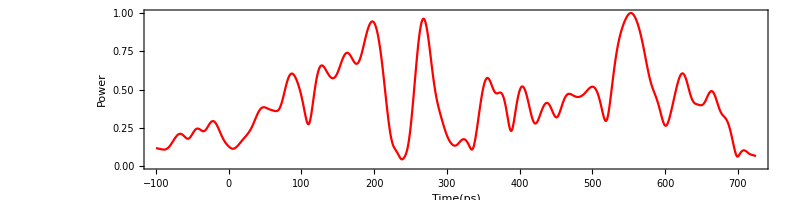

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

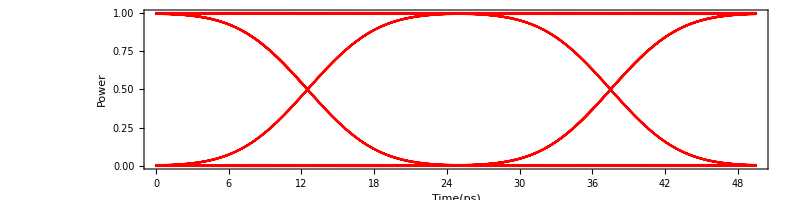

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

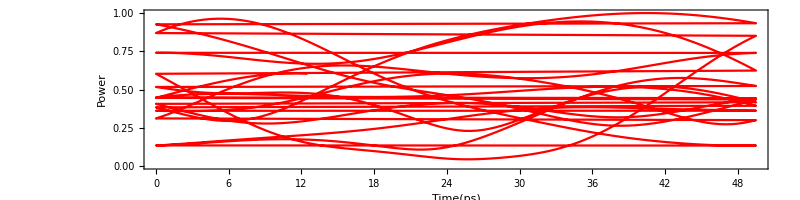

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 44 point

0 is 88 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.716006

Average of 0 is 0.310828

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.119542

A Standard Deviation of 0 is 0.144082

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-1255.15]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

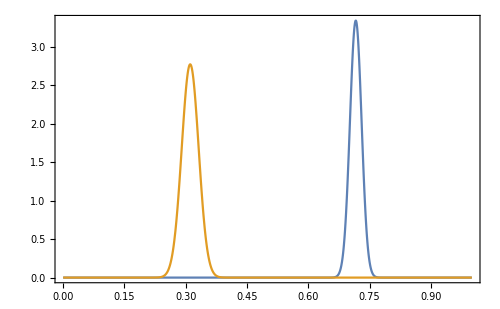

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 1.53695

Q-dB is 3.73321 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.0621524

Eye Opening is 0.349362

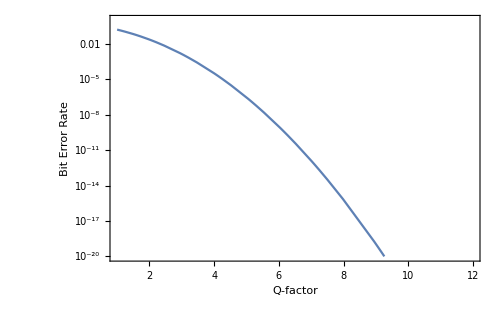

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```